```mathematica
ClearAll["Global`x"];
Fod = (m*v^2)/R;
Fg= m * g;
```

```mathematica
Ep1 = m*g*H;
Ep2 = m*g * (2 * R);
Ek2 = (m * v^2)/2;
```

```mathematica
r1 = Solve[{Fod == Fg, Ep1-Ep2 == Ek2}, {H, v}]
```

{{H→(5 R)/2,v→-√g √R},{H→(5 R)/2,v→√g √R}}

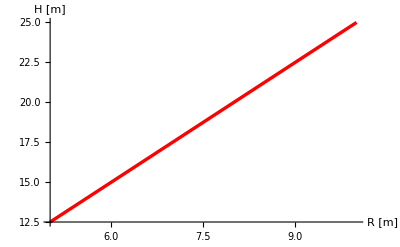

```mathematica
Plot[H/.r1[[1,1]],{R,5,10},
TextStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
 PlotStyle->{{RGBColor[1,0,0],Thickness[0.006]}},
AxesLabel->{"R [m]","H [m]"}]
```

```mathematica
ClearAll["Global`x"];

zuk=(vo^2×sin(2×α °))/g;
huk=(vo^2×sin^2(α °))/(2×g);
zpoz=v2×√((2×huk)/g);
```

```mathematica
s=1/2×zuk+zpoz;
```

```mathematica
rys1=Plot[s×10^-3/.x->0.2,{vo,100,200},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     x = 0.2  ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v_o [m/s]","s [km] "}]
```

-Graphics-

```mathematica
rys2=Plot[s×10^-3/.x->0.4,{vo,100,200},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     x = 0.4  ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v_o [m/s]","s [km] "}]
```

-Graphics-